# The Traveler's Dilemma

Text from:
http://jeremyclark.wordpress.com/2007/06/11/randomized-travelers-dilemma/

In the June 2007 issue, Scientific American ran a fantastic article on the Traveler’s Dilemma. The traveler’s dilemma is summarized as follows, 

"Lucy and Pete, returning from a remote Pacific island, find that the airline has damaged the identical antiques that each had purchased. An airline manager says that he is happy to compensate them but is handicapped by being clueless about the value of these strange objects. Simply asking the travelers for the price is hopeless, he figures, for they will inflate it. Instead he devises a more complicated scheme.He asks each of them to write down the price of the antique as any dollar integer between 2 and 100 without conferring together. If both write the same number, he will take that to be the true price, and he will pay each of them that amount. But if they write different numbers, he will assume that the lower one is the actual price and that the person writing the higher number is cheating. In that case, he will pay both of them the lower number along with a bonus and a penalty–the person who wrote the lower number will get $2 more as a reward for honesty and the one who wrote the higher number will get $2 less as a punishment. For instance, if Lucy writes 46 and Pete writes 100, Lucy will get $48 and Pete will get $44.

"What numbers will Lucy and Pete write? What number would you write?"

For reasons that you can get from reading the article (or thinking hard), the rational choice for Pete and Lucy is to write is 2. Of course, in practice, most people don’t follow the chain of reasoning that leads to this choice and instead choose a number close to 100. And so long as both participants ignore the rationale, they tend to make more money. 

Exactly why the rational answer, dictated by game theory, breaks down is subject to interpretation. In describing how game theory is applied to auctions, Tim Harford notes that “auctions require ‘if he thinks that she thinks that I think that he thinks’ chains of reasoning that tend to have weak links. Those links can easily break if any bidder has any reason to suspect that any other bidder is irrational.”
          
From how real people play the traveler’s dilemma, the links here tend to break down as well. Its only rational to drop your number if you reasonably suspect the other player will drop hers. At the same time, you want to take advantage of the chance that she won’t because you both will do well if she is less rational than you (which might make her more rational, as she will do better too).

There are a few cognitive biases that may come into play here. The first is that while you know you are rational, you are less than certain if the other player is. Assuming she is not rational is risky, but it is a risk that offers a potentially higher reward.In the base case (a number between 2 and 100, and a penalty/reward of $2), assume for simplicity that the other player is either rational and will write down 2, or irrational and will write down 100. By writing down 2 yourself, you are certain to get $2. By writing down $100, you risk getting $0 or $100. Behavioral economists have studied a similar type of scenario where someone is offered the choice between, say, $2 now or flipping a coin where heads will give you nothing and tails will give you, say, $4.The expected value in this case is equivalent, but the average human will take the sure bet. Where the study of risk aversion gets interesting is when you play with the numbers and offer $5 or $6 or $10 on a tails, and see how high you have to make it before people take the bet. If it were an option between a certain $2, or a 50% chance at $100--I bet most of you would take it. Which is perhaps why most people take the risk that the other participant will act irrationally in the traveler’s dilemma.

Of course, the probability that they will act irrationally is not a 50-50 coin flip. It is unknowable. But what we can do is calculate what the minimum probability would have to be for the risk to have the same expected value as the outcome, and it is 2 %.In other words, if there is at least a 2% chance that the other participant will act irrationally and write down 100, then its rational to write down 100 yourself. This is simplified to two cases (they either write down 2 or 100) but reasoning holds even if you allow for them to be semi - rational (choose a number in the 90 s, or in above the 60 s, et cetera). Furthermore, all the empirical studies of the traveler’s dilemma give information on just how how rational the other player is likely to be–and so its no longer a blind guess. Of course, terming the strategy of writing down 100 with the word “irrational” is a misnomer. True irrational behavior would have no strategy at all, and such a player would just write down a random number. I played the traveler’s dilemma with my computer acting as a random player (and with a minor change of rules: a number between 80 and 200, and a penalty of 5). This graph shows how much I won (on average for one round) for every possible number I could write down (80, 81, …, 198, 199, 200). As you can see, against a random opponent, I am best writing down a number close but just under 200.

## Constant Penalty

```mathematica
Needs["PlotLegends`"]
```

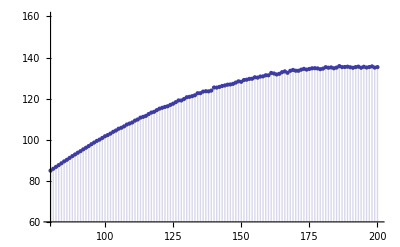

```mathematica
(* Parameters: games are the number of iterations. The graph will become more accurate as increased. penalty is set to 5 *)

games=10000;
penalty = 5;

(* Code *)
fa[x_,p_]:=x[[1]]/;x[[1]]==x[[2]]
fa[x_,p_]:=x[[2]]-p/;x[[1]]>x[[2]]
fa[x_,p_]:=x[[1]]+p/;x[[1]]<x[[2]]
g[c_,p_]:=N[Total[fa[#1,p]&/@Transpose[{Table[c,{games}],RandomInteger[{80,200},games]}]]/games]
h[p_]:=Transpose[{Range[80,200],g[#,p]&/@Range[80,200]}];

ListPlot[h[penalty],PlotRange->{60,160},Filling->Axis]
```

## Variable Penalties

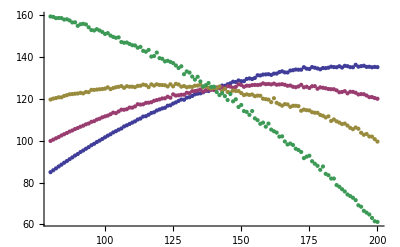

```mathematica
ListPlot[{h[5],h[20],h[40],h[80]}]
```

Blue is the same graph as the first one (a penalty of 5), purple is 20, gold is forty, and green is 80. As you can see, the optimal number to write down decreases as the penalty increases.When the penalty reaches a maximum of 80, you are not only best playing the safe number–you actually make more than in any other configuration. In real-life, players are likely to be somewhere between perfectly rational and random. But the two general behaviors in the simplified examples (risking that the other player will act irrationally, and decreasing your number as the penalty increases) are behaviors exhibited in real-world user studies.